```mathematica
Needs["Utilities`FilterOptions`"](*use FilterRules instead.*)
```

Get::noopen: Cannot open Utilities`FilterOptions`.

Needs::nocont: Context Utilities`FilterOptions` was not created when Needs was evaluated.

$Failed

```mathematica
opts
```

Sequence[opt1→w,opt2→y,opt3→z,opt4→42]

```mathematica
okayOpts=FilterRules[List[opts],Options[f]]
```

{opt1→w,opt2→y}

```mathematica
Options[fitPlot]={InterpolationOrder->3};
Clear[fitPlot];
this:fitPlot[data_?MatrixQ,opts___?OptionQ]:=Module[
{valid,order,optslist,plotOpts,listplotOpts,gfxOpts,f,p,lp,x,n},
valid=First/@Union[Options[Plot],Options[ListPlot],Options[Graphics]];(*合法的选项*)
optslist=Flatten[{opts}];(*所有的选项*)
Scan[
If[!MemberQ[valid,First[#]],
Message[f::optx,ToString[First[#]],ToString[Unevaluated[this]]]]&,
optslist];(*扫描一遍，出现不合法的给出消息提示*)
order=InterpolationOrder/.{opts}/.Options[fitPlot];
plotOpts=FilterRules[optslist,Options[Plot]];
listplotOpts=FilterRules[optslist,Options[ListPlot]];
gfxOpts=FilterRules[optslist,Options[Graphics]];
Print[{order,optslist,plotOpts,listplotOpts,gfxOpts}];
lp=ListPlot[data,DisplayFunction->Identity,listplotOpts];
f=Fit[data,Table[x^n,{n,0,order}],x];
p=Plot[f,
Evaluate[{x,data[[1,1]],Last[data][[1]]}],
DisplayFunction->Identity,
Evaluate[plotOpts]
];
Show[p,lp,DisplayFunction->$DisplayFunction,gfxOpts]
]
```

```mathematica
pts=Table[{i,Sin[2i]+(Random[]-.5)/5},{i,0,3,.1}];
```

f$31024::optx: Unknown option a in fitPlot[{{0., -0.0616097}, {0.1, 0.271041}, {0.2, 0.438208}, {0.3, 0.572233}, {0.4, 0.629955}, {0.5, 0.821785}, {0.6, 0.862257}, {0.7, 1.04367}, {0.8, 0.955703}, {0.9, 0.882233}, {1., 0.948199}, {1.1, 0.825103}, {1.2, 0.670087}, {1.3, 0.419953}, {1.4, 0.261057}, {1.5, 0.167224}, {1.6, 0.0301377}, {1.7,…0.550767}, {2., -0.724316}, {2.1, -0.840555}, {2.2, -0.952532}, {2.3, -0.996038}, {2.4, -1.00207}, {2.5, -0.900274}, {2.6, -0.833174}, {2.7, -0.682702}, {2.8, -0.649769}, {2.9, -0.486266}, {3., -0.259353}}, InterpolationOrder -> 4, PlotPoints -> 20, Frame -> True, PlotStyle -> PointSize[0.03], a -> 10].

{4,{InterpolationOrder→4,PlotPoints→20,Frame→True,PlotStyle→PointSize[0.03],a→10},{PlotPoints→20,Frame→True,PlotStyle→PointSize[0.03]},{InterpolationOrder→4,Frame→True,PlotStyle→PointSize[0.03]},{Frame→True}}

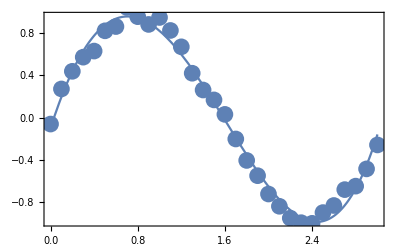

```mathematica
fitPlot[pts,
InterpolationOrder->4,
PlotPoints->20,
Frame->True,
PlotStyle->PointSize[.03],a->10]
```

```mathematica
fitPlot[pts,
InterpolationOrder->4,
PlotPoints->20,
Frame->True,
PlotStyle->PointSize[.03]]
```

{4,{InterpolationOrder→4,PlotPoints→20,Frame→True,PlotStyle→PointSize[0.03]},{PlotPoints→20,Frame→True,PlotStyle→PointSize[0.03]},{InterpolationOrder→4,Frame→True,PlotStyle→PointSize[0.03]},{Frame→True}}

-Graphics-